```mathematica
cwMatrix[n_,a_,b_,c_,d_]:=Table[Which[j==i,1,j==i+1,a,j==i+2,c,j==i-1,b,j==i-2,d,True,0],{i,n},{j,n+1}];
```

```mathematica
cw1=cwMatrix[15,a,0,0,0]
```

(1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | a)

```mathematica
mcw=cw1//NullSpace
```

(a^15 | -a^14 | a^13 | -a^12 | a^11 | -a^10 | a^9 | -a^8 | a^7 | -a^6 | a^5 | -a^4 | a^3 | -a^2 | a | -1)

```mathematica
generateMatrix[n_,a_,b_,c_,d_]:=Table[Which[j==i,a^((-1)^(j)j),j==i+1,a^((-1)^(j)j),j==i+2,c,j==i-1,b,j==i-2,d,True,0],{i,n},{j,n+1}];

(*Example usage with your substitution:a=1,b=1,c=1*)
m1=generateMatrix[15,a,0,0a^2,0/a^2]
```

(1/a | a^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a^2 | 1/a^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/a^3 | a^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a^4 | 1/a^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/a^5 | a^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a^6 | 1/a^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/a^7 | a^8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a^8 | 1/a^9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/a^9 | a^10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^10 | 1/a^11 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/a^11 | a^12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^12 | 1/a^13 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/a^13 | a^14 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^14 | 1/a^15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/a^15 | a^16)

```mathematica
m2=m1 //NullSpace
```

(a^17 | -a^14 | a^19 | -a^12 | a^21 | -a^10 | a^23 | -a^8 | a^25 | -a^6 | a^27 | -a^4 | a^29 | -a^2 | a^31 | -1)

```mathematica
m3=m2[[1]]/.a->2.0//Normalize
cwm3=mcw[[1]]/.a->2.0//Normalize
```

{0.000059097,-7.38713×10^-6,0.000236388,-1.84678×10^-6,0.000945553,-4.61696×10^-7,0.00378221,-1.15424×10^-7,0.0151288,-2.8856×10^-8,0.0605154,-7.21399×10^-9,0.242061,-1.8035×10^-9,0.968246,-4.50875×10^-10}

{0.866025,-0.433013,0.216506,-0.108253,0.0541266,-0.0270633,0.0135316,-0.00676582,0.00338291,-0.00169146,0.000845728,-0.000422864,0.000211432,-0.000105716,0.000052858,-0.000026429}

```mathematica
wongColors={RGBColor[0,0,0],(*black*)RGBColor[0.9,0.6,0],(*orange*)RGBColor[0.35,0.7,0.9],(*sky blue*)RGBColor[0,0.6,0.5],(*bluish green*)RGBColor[0.95,0.9,0.25],(*yellow*)RGBColor[0,0.45,0.7],(*blue*)RGBColor[0.8,0.4,0],(*vermillion*)RGBColor[0.8,0.6,0.7]}; (*reddish purple*) (*Color Scheme for Color Blind People.*)
```

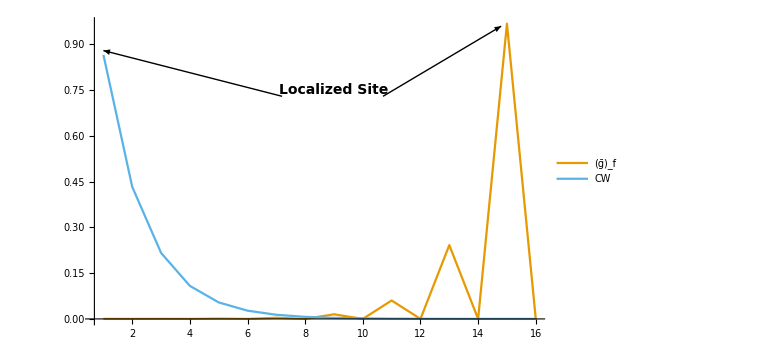
-Graphics-Magnitude of 0-Mode Eigenvector ComponentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[m3],Abs[cwm3]},Joined->True,PlotRange->All,PlotStyle->wongColors[[{2,3}]],(*orange and sky blue*)PlotLegends->Placed[Framed[LineLegend[wongColors[[{2,3}]],{"(ḡ)_f","CW"}],FrameStyle->Black,RoundingRadius->5,Background->White],Right],AxesLabel->{None,None},ImageSize->Large,Epilog->{Text[Style["Localized Site",14,Bold],{9,0.75},{0,1}],Arrow[{{7.2,0.73},{1,0.88}}],Arrow[{{10.7,0.73},{14.8,0.96}}]}],Style[Rotate["Magnitude of 0-Mode Eigenvector Components",90 Degree],14],Left],Style["Site",14],Bottom]
```

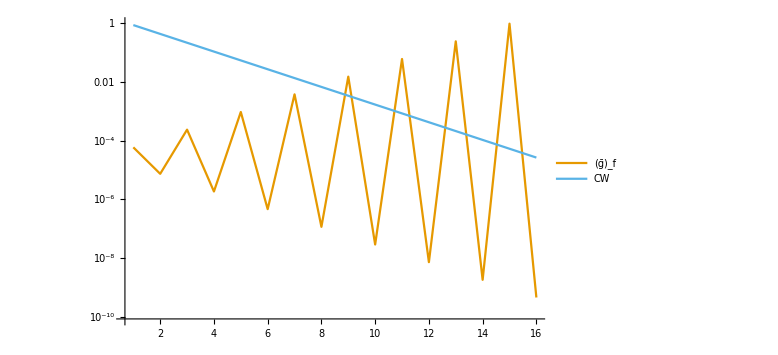
-Graphics-Log10 of Magnitude of 0-Mode Eigenvector ComponentsSite

```mathematica
Labeled[Labeled[ListLogPlot[{Abs[m3],Abs[cwm3]},Joined->True,PlotStyle->wongColors[[{2,3}]],(*orange& sky blue*)PlotLegends->Placed[Framed[LineLegend[wongColors[[{2,3}]],{"(ḡ)_f","CW"}],FrameStyle->Black,RoundingRadius->5,Background->White],Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,-12,2,2}]}],Style[Rotate["Log10 of Magnitude of 0-Mode Eigenvector Components",90 Degree],12],Left],Style["Site",14],Bottom]
```